```mathematica
data=ResourceData["Sample Data: Swiss Rainfall", "Data"]
```

SpatialPointData[…]

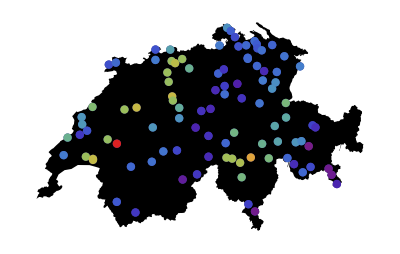

```mathematica
Show[Region[data["ObservationRegion"]],PointValuePlot[data,ColorFunction->"Rainbow"]]
```

```mathematica
spf=SpatialEstimate[data->"Rainfall",SpatialTrendFunction->1]
```

SpatialEstimate::novals: -- Message text not found --

SpatialEstimate[SpatialPointData[…]→Rainfall,SpatialTrendFunction→1]

```mathematica
spf=SpatialEstimate[data->"Rainfall",SpatialTrendFunction->1]
```

SpatialEstimate::novals: -- Message text not found --

SpatialEstimate[SpatialPointData[…]→Rainfall,SpatialTrendFunction→1]

```mathematica
data=SpatialPointData[…];
```